```mathematica
345^3
```

41063625

```mathematica
IntegerDigits[345^3]
```

{4,1,0,6,3,6,2,5}

```mathematica
Permutations[IntegerDigits[345^3]]
```

```mathematica
FromDigits/@Permutations[IntegerDigits[345^3]]
```

```mathematica
Select[IntegerQ[CubeRoot[#]]&][FromDigits/@Permutations[IntegerDigits[345^3]]]
```

{41063625,66430125,56623104}

```mathematica
Select[IntegerQ[CubeRoot[#]]&][FromDigits/@Permutations[IntegerDigits[345^3]]]//RepeatedTiming
```

{0.482009,{41063625,66430125,56623104}}

```mathematica
Sort[IntegerDigits[345^3]]
```

{0,1,2,3,4,5,6,6}

```mathematica
Sort[IntegerDigits[384^3]]
```

{0,1,2,3,4,5,6,6}

```mathematica
Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&[345,384]
```

True

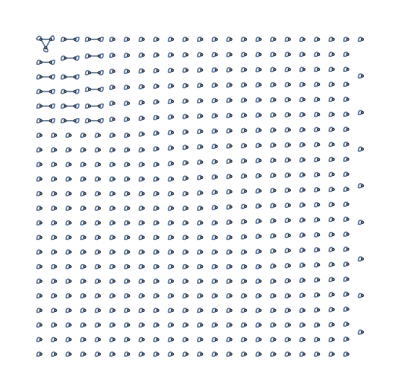

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[500]]
```

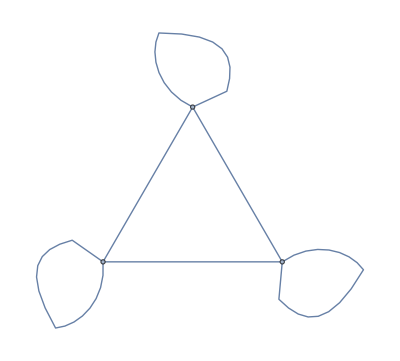
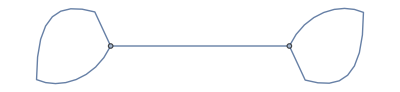
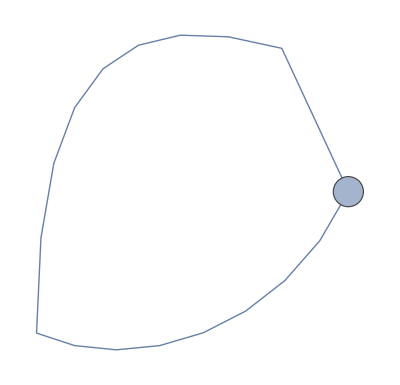
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ConnectedGraphComponents[RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[500]]]
```

```mathematica
TakeLargestBy[ConnectedGraphComponents[RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[500]]],VertexCount,1]
```

{-Graphics-}

```mathematica
First[TakeLargestBy[ConnectedGraphComponents[RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[500]]],VertexCount,1]]
```

-Graphics-

```mathematica
InputForm[First[TakeLargestBy[ConnectedGraphComponents[RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[500]]],VertexCount,1]]]
```

Graph[{345, 384, 405}, {Null, SparseArray[Automatic, {3, 3}, 0, 
   {1, {{0, 3, 5, 6}, {{1}, {2}, {3}, {2}, {3}, {3}}}, {1, 1, 1, 
    1, 1, 1}}]}]

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[1500]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[1500,2000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[2000,3000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[3000,5000]]
```

-Graphics-

```mathematica
Graph[#,VertexLabels->Automatic]&/@TakeLargestBy[ConnectedGraphComponents[-Graphics-],VertexCount,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[5000,6000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[6000,7000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[7000,9000]]
```

-Graphics-

```mathematica
Graph[TakeLargestBy[ConnectedGraphComponents[RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[7000,9000]]],VertexCount,1],VertexLabels->Automatic]
```

Graph[{-Graphics-},VertexLabels→Automatic]

```mathematica
Graph[-Graphics-,VertexLabels->Automatic]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[9000,9500]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[9500,10000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[10000,11000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[11000,12000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[12000,13000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[13000,14000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[14000,18000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[18000,25000]]
```

-Graphics-

```mathematica
First[TakeLargestBy[VertexCount,1]][%]
```

7001

```mathematica
TakeLargestBy[ConnectedGraphComponents@%407,VertexCount,1]
```

{-Graphics-}

```mathematica
ConstantArray[1,{5,5}]
```

{{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}

```mathematica
AdjacencyGraph[ConstantArray[1,{5,5}]]
```

-Graphics-

```mathematica
AdjacencyGraph[ConstantArray[1,{4,4}]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[25000,27000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[27000,30000]]
```

-Graphics-

```mathematica
RelationGraph[Sort[IntegerDigits[#1^3]]==Sort[IntegerDigits[#2^3]]&,Range[30000,40000]]
```

```mathematica
TakeLargestBy[ConnectedGraphComponents[%],VertexCount,100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Take[%417,2]
```

{-Graphics-,-Graphics-}

```mathematica
Graph[#,VertexLabels->Automatic]&/@%
```

{-Graphics-,-Graphics-}

```mathematica
VertexList/@%
```

{{33828,37671,37791,38103,39534},{31196,32186,33236,36137,37046}}

```mathematica
Min/@%
```

{33828,31196}

```mathematica
31196^3
```

30359648217536

```mathematica
31196^3
```

30359648217536

```mathematica
32186^3
```

33342719650856

```mathematica
Sort[IntegerDigits[32186^3]]
```

{0,1,2,3,3,3,4,5,5,6,6,7,8,9}

```mathematica
Sort[IntegerDigits[31196^3]]
```

{0,1,2,3,3,3,4,5,5,6,6,7,8,9}

```mathematica
SameQ@@{Sort[IntegerDigits[31196^3]],Sort[IntegerDigits[32186^3]]}
```

True